# Optimización de Redes Bayesianas por Algoritmo Genético

### Autor: Carlos Manuel Rodríguez Martínez E-Mail: fis.carlosmanuel@gmail.com

## Resumen

Se implementa un algoritmo capaz de buscar el mejor modelo bajo la métrica MDL (Minimum Description Length), la cual mide qué tan bien se comprime un conjunto de datos bajo un modelo. El algoritmo procede a generar todos los DAG y evaluar la puntuación MDL dado un conjunto de datos. Se selecciona el grafo con menos puntuación MDL como el mejor modelo para describir los datos.

Referencia:
Levine, Nicholas D., “Using Minimum Description Length for Discretization Classification of Data Modeled by Bayesian Networks” (2011). Applied Mathematics Graduate Theses & Dissertations. 21. 
https://scholar.colorado.edu/appm_gradetds/21

## Generación de población

```mathematica
RemoveDiagonal[matrix_]:=Table[If[i ≠ j,matrix[[i,j]],0],{i,1,Length[matrix]},{j,1,Length[First[matrix]]}];
```

```mathematica
BuildMatrix[paramList_,n_]:=Block[{parts},
parts = Partition[paramList,n-1];
RemoveDiagonal[Table[Insert[parts[[i]],1,i],{i,1,n}]]
];
```

```mathematica
GeneratePopulationSeed[n_,size_]:=Map[BuildMatrix[#,n]&,RandomSample[Tuples[{0,1},n(n-1)],size]];
```

```mathematica
CheckComplex[l_]:=Apply[Or,Map[MatchQ[#,_Complex]&,l]];
CheckNegative[l_]:=Apply[Or,Map[Re[#]≤0&,l]];
IsDAG[matrix_]:=Block[{ev},
If[Tr[matrix]≠0,Return[False]];
ev = N[Eigenvalues[matrix+IdentityMatrix[Length[matrix]]]];
If[CheckNegative[ev] || CheckComplex[ev],
Return[False],
Return[True]
];
];

RemoveRandomVertex[matrix_]:=Block[{vector,removedIndex},
vector = Flatten[matrix];
removedIndex = RandomChoice[Position[vector,1]];
Partition[ReplacePart[vector,First[removedIndex]->0],Length[matrix]]
];
SimplifyToDAG[matrix_]:=Block[{},
If[IsDAG[matrix],
matrix
,
SimplifyToDAG[RemoveRandomVertex[matrix]]
]
];
```

```mathematica
GeneratePopulation[n_,size_]:=Block[{populationSeed,dag},
populationSeed = GeneratePopulationSeed[n,size];
dag = Map[SimplifyToDAG,populationSeed];
Return[dag];
];
```

## Cálculo de rendimiento

A continuación se evalúan los DAG a partir de la métrica MDL que toma en cuenta la contribución a la longitud de la descripción de tres aspectos del modelo.

La contribución de las variables:

||X_i|| representa el número de valores diferentes que puede tomar la variable X. La contribución del DAG:

|Π_i| la cantidad de padres de X_i. La contribución de los parámetros:

||Π_i|| representa el número de configuraciones posibles de los padres de X_i. En total la contribución del modelo a la longitud de descripción es:

Por último es necesario calcular la contribución de los datos dado el modelo. El modelo está implícito en esta cálculo debido a que la probabilidad p(u_i) se calcula haciendo uso del DAG.

```mathematica
Parents[graph_,vertex_]:=Cases[graph, p_->vertex:>p];
PossibleValues[dataset_,attribute_]:=DeleteDuplicates[dataset[[All,attribute]]];
ParentConfigurations[dataset_,parents_]:=Tuples[Map[PossibleValues[dataset,#]&,parents]];
NodeParentConfigurations[dag_,dataset_,node_]:=ParentConfigurations[dataset,Parents[dag,node]];

VariablesDL[dataset_]:=Block[{n = Length[First[dataset]]},
Sum[Log[Length[PossibleValues[dataset,i]]],{i,1,n}]+Log[n]
];

DAGDL[dag_]:=Block[{n = Length[VertexList[dag]]},
If[dag == {},Return[0]];
Log[n]*Sum[1+Length[Parents[dag,i]],{i,1,n}]
];
ParameterDL[dag_,dataset_]:=Block[{n = Length[First[dataset]],m=Length[dataset]},
1/2 Log[m]*Sum[Length[NodeParentConfigurations[dag,dataset,i]]*(Length[PossibleValues[dataset,i]]-1),{i,1,n}]
];
ModelDL[dag_,dataset_]:=VariablesDL[dataset] + DAGDL[dag] + ParameterDL[dag,dataset];
```

```mathematica
AttributeValues[dag_,data_,attribute_]:=Block[{parents},
parents = Parents[dag,attribute];
Map[<|"ParentValues"->#[[parents]],"Value"->#[[attribute]]|>&,data]
];
AttributeProbability[dag_,data_,node_,nodeValue_,parentValues_]:=Block[{num,den},
num = Length[Cases[AttributeValues[dag,data,node],KeyValuePattern[{"ParentValues"->parentValues, "Value"->nodeValue}]]];
den = Length[Cases[AttributeValues[dag,data,node],KeyValuePattern["ParentValues"->parentValues]]];
If[den ≠ 0,
Return[num/den];
,
Return[0]
];
];

InstanceProbability[dag_,dataset_,instance_]:=Block[{n= Length[First[dataset]]},
Apply[Times,Table[AttributeProbability[dag,dataset,i,instance[[i]],instance[[Parents[dag,i]]]],{i,1,n}]]
];

DataDL[dag_,dataset_]:=-Total[Map[Log[InstanceProbability[dag,dataset,#]]&,dataset]];
MDLScore[dag_,dataset_]:=ModelDL[dag,dataset] + DataDL[dag,dataset];
```

### Ejemplo

```mathematica
testData = Drop[Import[FileNameJoin[{NotebookDirectory[],"BayesMDL","data3.dat"}]],1];
```

```mathematica
MDLScore[{1->2},testData]
```

6 Log[2]+331 Log[25000/11523]+Log[3]+14 Log[25000/5727]+Log[62500/12191]+145 Log[62500/6059]+7 Log[125000/581]+2 Log[62500/167]+2 Log[500]

```mathematica
EvaluateGenome[testData_,population_]:=ProgressParallelMap[
<|
"Genome"->#,
"MDL"->N@MDLScore[EdgeList[AdjacencyGraph[#]],testData]
|>&,
population,
"Label"->"Evaluating population",
Method->"CoarsestGrained"
];
```

## Selección

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateSelection[evaluatedGenome_,n_]:= Part[SortBy[evaluatedGenome,Key["MDL"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]]
```

## Crossover

```mathematica
RandomCrossover[parent1_,parent2_]:=Block[{vector1,vector2,transformed},
vector1 =Flatten[parent1];
vector2 =Flatten[parent2];
transformed = Table[If[RandomInteger[]==1,vector1[[i]],vector2[[i]]],{i,1,Length[vector1]}];
SimplifyToDAG[Partition[transformed,Length[parent1]]]
];
```

```mathematica
PopulationCrossover[population_,childrenPerCouple_]:=Block[{couples,newGeneration},
couples = Partition[RandomSample[population],2];
newGeneration = Flatten[
Map[
Table[RandomCrossover[First[#],Last[#]],childrenPerCouple]&,
couples
],1];
Return[newGeneration];
];
```

## Mutación

```mathematica
Flip[0]=1;
Flip[1] = 0;

RandomMutate[matrix_,probability_]:=Block[{newList,index,newMatrix},
If[RandomReal[]<probability,
newList = Flatten[matrix];
index = RandomInteger[{1,Length[newList]}];
newList = MapAt[Flip,newList, index];
newMatrix = Partition[newList,Length[matrix]];
Return[SimplifyToDAG[newMatrix]];
,
Return[matrix]
]
];
PopulationMutate[population_,probability_]:=Map[RandomMutate[#,probability]&,population];
```

```mathematica
MatrixForm[RandomMutate[individual,1]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
individual = First@GeneratePopulation[4,1]
```

{{0,1,0,0},{0,0,0,0},{1,0,0,0},{1,0,0,0}}

## Algoritmo principal

```mathematica
Needs["AdvancedMapping`"];

Generation[testData_,population_,survivors_,childrenPerCouple_,mutationProb_]:=Block[{evaluated,fittest,newGeneration},
evaluated = EvaluateGenome[testData,population];
fittest = ProportionateSelection[evaluated,survivors];
newGeneration = PopulationCrossover[fittest[[All,"Genome"]],childrenPerCouple];
PopulationMutate[newGeneration,mutationProb]
];
GeneticAlgorithm[testData_,population_,survivors_,childrenPerCouple_,mutationProb_,generations_]:=
NestList[Generation[testData,#,survivors,childrenPerCouple,mutationProb]&,population,generations];

SelectBest[testData_,population_]:=First@MinimalBy[EvaluateGenome[testData,population],Key["MDL"]];
```

```mathematica
population = GeneratePopulation[3,20];
```

```mathematica
generations = GeneticAlgorithm[testData,population,4,10,0.1,20];
```

```mathematica
best = ProgressMap[SelectBest[testData,#]&,generations];
```

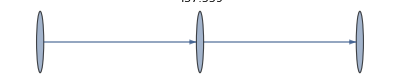
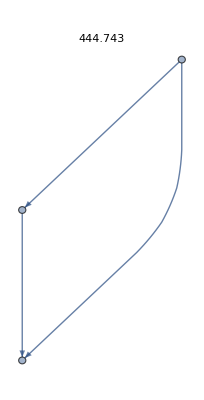
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[AdjacencyGraph[#["Genome"],PlotLabel->#["MDL"]]&,best]
```